```mathematica
ClearAll["Global`*"]
```

## Pauli matrices in z-base representation

|+z>=(1,0)
|-z>=(0,1)

```mathematica
Subscript[σ, axis_][ve_,ho_]:=axis,1({{0, 1}, {1, 0}})[[ve,ho]]+axis,2({{0, -ⅈ}, {ⅈ, 0}})[[ve,ho]]+axis,3({{1, 0}, {0, -1}})[[ve,ho]];
Id[ve_,ho_]:=ve,ho
```

```mathematica
{Table[Subscript[σ, 1][ve,ho],{ve,1,2},{ho,1,2}],Table[Subscript[σ, 2][ve,ho],{ve,1,2},{ho,1,2}],Table[Subscript[σ, 3][ve,ho],{ve,1,2},{ho,1,2}]};
Map[MatrixForm,%,1]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

## System Hamiltonian

Three coupled two-level systems,
1. Each spin has two energy levels ω_P apart, |+z_P> has ω_P/2 and |-z_P> has -ω_P/2.
2. Each pair of spins are coupled together with ω_PQ such that
	i. having the same spin is high energy (+ω_PQ/2).
	ii. having opposite spins is slightly lower energy (-ω_PQ/2).

```mathematica
HsSep[veL_,hoL_,veM_,hoM_,veR_,hoR_]:=
ℏ(ωL/2 Subscript[σ, 3][veL,hoL]Id[veM,hoM]Id[veR,hoR]+
ωM/2 Id[veL,hoL]Subscript[σ, 3][veM,hoM]Id[veR,hoR]+
ωR/2 Id[veL,hoL]Id[veM,hoM]Subscript[σ, 3][veR,hoR]+
ωLM/2 Subscript[σ, 3][veL,hoL]Subscript[σ, 3][veM,hoM]Id[veR,hoR]+
ωMR/2 Id[veL,hoL]Subscript[σ, 3][veM,hoM]Subscript[σ, 3][veR,hoR]+
ωRL/2 Subscript[σ, 3][veL,hoL]Id[veM,hoM]Subscript[σ, 3][veR,hoR])
```

Eigenstates,
|1> =|+z,+z,+z>
|2> =|+z,+z,-z>
|3> =|+z,-z,+z>
|4> =|+z,-z,-z>
|5> =|-z,+z,+z>
|6> =|-z,+z,-z>
|7> =|-z,-z,+z>
|8> =|-z,-z,-z>

Eigenstate mapping function, (maps overall state (1 to 8) to subsystem state  (|±z_P>),

```mathematica
EmapL[i_]:=(i,5+i,6+i,7+i,8)2+(i,1+i,2+i,3+i,4)1
EmapM[i_]:=(i,3+i,4+i,7+i,8)2+(i,1+i,2+i,5+i,6)1
EmapR[i_]:=(i,2+i,4+i,6+i,8)2+(i,1+i,3+i,5+i,7)1
```

Matrix form of the Hamiltonian,

```mathematica
Hs[ve_,ho_]:=HsSep[EmapL[ve],EmapL[ho],EmapM[ve],EmapM[ho],EmapR[ve],EmapR[ho]]
```

```mathematica
HsMatrix=Table[Hs[ve,ho],{ve,1,8},{ho,1,8}];
MatrixForm[HsMatrix]
HsEVal[i_]:=(Eigenvalues[HsMatrix][[{8,1,7,2,4,5,3,6}]])[[i]]
HsEVec[i_]:=(Eigenvectors[HsMatrix][[{8,1,7,2,4,5,3,6}]])[[i]]
```

((ωL/2+ωLM/2+ωM/2+ωMR/2+ωR/2+ωRL/2) ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (ωL/2+ωLM/2+ωM/2-ωMR/2-ωR/2-ωRL/2) ℏ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (ωL/2-ωLM/2-ωM/2-ωMR/2+ωR/2+ωRL/2) ℏ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (ωL/2-ωLM/2-ωM/2+ωMR/2-ωR/2-ωRL/2) ℏ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (-ωL/2-ωLM/2+ωM/2+ωMR/2+ωR/2-ωRL/2) ℏ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (-ωL/2-ωLM/2+ωM/2-ωMR/2-ωR/2+ωRL/2) ℏ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (-ωL/2+ωLM/2-ωM/2-ωMR/2+ωR/2-ωRL/2) ℏ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (-ωL/2+ωLM/2-ωM/2+ωMR/2-ωR/2+ωRL/2) ℏ)

## Pauli matrices in compound system representation

Since the system Hamiltonian is diagonal, its eigenvectors are just the different unit vectors in 8-dimensions.

```mathematica
Subscript[σ, P_,axis_][ve_,ho_]:=Subscript[σ, P,axis][ve,ho]=
P,1(Subscript[σ, axis][EmapL[ve],EmapL[ho]]Id[EmapM[ve],EmapM[ho]]Id[EmapR[ve],EmapR[ho]])+
P,2(Id[EmapL[ve],EmapL[ho]]Subscript[σ, axis][EmapM[ve],EmapM[ho]]Id[EmapR[ve],EmapR[ho]])+
P,3(Id[EmapL[ve],EmapL[ho]]Id[EmapM[ve],EmapM[ho]]Subscript[σ, axis][EmapR[ve],EmapR[ho]])

Subscript[σmatrix, P_,axis_]:=Subscript[σmatrix, P,axis]=Table[Subscript[σ, P,axis][ve,ho],{ve,1,8},{ho,1,8}]
Subscript[σPmatrix, P_]:=1/2(Subscript[σmatrix, P,1]+ⅈ Subscript[σmatrix, P,2])
Subscript[σMmatrix, P_]:=1/2(Subscript[σmatrix, P,1]-ⅈ Subscript[σmatrix, P,2])
```

```mathematica
{MatrixForm[Subscript[σmatrix, 1,1]],MatrixForm[Subscript[σmatrix, 2,1]],MatrixForm[Subscript[σmatrix, 3,1]]}
{MatrixForm[Subscript[σmatrix, 1,2]],MatrixForm[Subscript[σmatrix, 2,2]],MatrixForm[Subscript[σmatrix, 3,2]]}
{MatrixForm[Subscript[σmatrix, 1,3]],MatrixForm[Subscript[σmatrix, 2,3]],MatrixForm[Subscript[σmatrix, 3,3]]}
{MatrixForm[Subscript[σPmatrix, 1]],MatrixForm[Subscript[σPmatrix, 2]],MatrixForm[Subscript[σPmatrix, 3]]}
{MatrixForm[Subscript[σMmatrix, 1]],MatrixForm[Subscript[σMmatrix, 2]],MatrixForm[Subscript[σMmatrix, 3]]}
```

{(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

{(0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0),(0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0),(0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0)}

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

{(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

## Assumptions about the spectrum of the system Hamiltonian

Uniqueness assumption (Dummy ω values to get unique eigenvalues),

```mathematica
ωassum={ωL==10,ωM==0.1,ωR==0.0001,ωLM==1.01,ωMR==1,ωRL==0.001,ℏ==1};
ωassum1=Flatten[{Table[Subscript[ω, {i,j}]->(HsEVal[i]-HsEVal[j] )/ℏ,{i,1,8},{j,1,8}]}];
```

```mathematica
MatrixForm[Simplify[HsMatrix ,Assumptions->ωassum]]
```

(6.05555 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5.05445 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3.94555 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4.94445 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -4.95545 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -5.95455 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -5.04545 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.04455)

## Corresponding transition frequencies

Transition frequencies,

```mathematica
ω[m_,n_]:=Simplify[(HsEVal[m]-HsEVal[n])/ℏ]
```

Unique and positive transition frequencies,

```mathematica
ω[i_]:=Module[{temp1,temp2,temp3},
temp1=Flatten[Table[ω[m,n],{m,2,8},{n,1,m-1}]];
temp2=Simplify[temp1,Assumptions->ωassum];
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp1 temp3,0][[i]]
]
ωsize:=Module[{temp1,temp2,temp3},
temp1=Flatten[Table[ω[m,n],{m,2,8},{n,1,m-1}]];
temp2=Simplify[temp1,Assumptions->ωassum];
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
Dimensions[DeleteCases[temp1 temp3,0]][[1]]
]
ωplus[i_]:=Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[Table[HsEVal[m],{m,2,8},{n,1,m-1}]];
temp1=Flatten[Table[ω[m,n],{m,2,8},{n,1,m-1}]];
temp2=Simplify[temp1,Assumptions->ωassum];
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp0 temp3,0][[i]]
]
ωminus[i_]:=Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[Table[HsEVal[n],{m,2,8},{n,1,m-1}]];
temp1=Flatten[Table[ω[m,n],{m,2,8},{n,1,m-1}]];
temp2=Simplify[temp1,Assumptions->ωassum];
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp0 temp3,0][[i]]
]
```

List all transition frequencies

```mathematica
Table[ω[i],{i,1,ωsize}]
ωsize
```

{-ωMR-ωR-ωRL,-ωLM-ωM-ωMR,-ωLM-ωM+ωR+ωRL,-ωLM-ωM-ωR-ωRL,-ωLM-ωM+ωMR,ωMR-ωR-ωRL,-ωL-ωLM-ωRL,-ωL-ωLM+ωMR+ωR,-ωL+ωM+ωMR-ωRL,-ωL+ωM+ωR,-ωL-ωLM-ωMR-ωR,-ωL-ωLM+ωRL,-ωL+ωM-ωR,-ωL+ωM-ωMR+ωRL,-ωMR-ωR+ωRL,-ωL-ωM-ωMR-ωRL,-ωL-ωM+ωR,-ωL+ωLM-ωRL,-ωL+ωLM-ωMR+ωR,ωLM-ωM-ωMR,ωLM-ωM+ωR-ωRL,-ωL-ωM-ωR,-ωL-ωM+ωMR+ωRL,-ωL+ωLM+ωMR-ωR,-ωL+ωLM+ωRL,ωLM-ωM-ωR+ωRL,ωLM-ωM+ωMR,ωMR-ωR+ωRL}

28

## Density matrix for the system

Full density matrix is required, since driving field Hamiltonian provides non-diagonal interactions,

```mathematica
ρMatrix[t]=Table[Subscript[ρ, {i,j}][t],{i,1,8},{j,1,8}];
MatrixForm[%]
```

(ρ_{1,1}[t] | ρ_{1,2}[t] | ρ_{1,3}[t] | ρ_{1,4}[t] | ρ_{1,5}[t] | ρ_{1,6}[t] | ρ_{1,7}[t] | ρ_{1,8}[t]
ρ_{2,1}[t] | ρ_{2,2}[t] | ρ_{2,3}[t] | ρ_{2,4}[t] | ρ_{2,5}[t] | ρ_{2,6}[t] | ρ_{2,7}[t] | ρ_{2,8}[t]
ρ_{3,1}[t] | ρ_{3,2}[t] | ρ_{3,3}[t] | ρ_{3,4}[t] | ρ_{3,5}[t] | ρ_{3,6}[t] | ρ_{3,7}[t] | ρ_{3,8}[t]
ρ_{4,1}[t] | ρ_{4,2}[t] | ρ_{4,3}[t] | ρ_{4,4}[t] | ρ_{4,5}[t] | ρ_{4,6}[t] | ρ_{4,7}[t] | ρ_{4,8}[t]
ρ_{5,1}[t] | ρ_{5,2}[t] | ρ_{5,3}[t] | ρ_{5,4}[t] | ρ_{5,5}[t] | ρ_{5,6}[t] | ρ_{5,7}[t] | ρ_{5,8}[t]
ρ_{6,1}[t] | ρ_{6,2}[t] | ρ_{6,3}[t] | ρ_{6,4}[t] | ρ_{6,5}[t] | ρ_{6,6}[t] | ρ_{6,7}[t] | ρ_{6,8}[t]
ρ_{7,1}[t] | ρ_{7,2}[t] | ρ_{7,3}[t] | ρ_{7,4}[t] | ρ_{7,5}[t] | ρ_{7,6}[t] | ρ_{7,7}[t] | ρ_{7,8}[t]
ρ_{8,1}[t] | ρ_{8,2}[t] | ρ_{8,3}[t] | ρ_{8,4}[t] | ρ_{8,5}[t] | ρ_{8,6}[t] | ρ_{8,7}[t] | ρ_{8,8}[t])

## Interaction Hamiltonian with (classically modelled) Driving Field

Assume for simplicity,
1. Only the M spin is non-zero (ω_L=ω_R=0).
2. L and R is non interacting with the electric field.

There is an coherent electrical field of frequency ωF interacting with the system,
1. Interaction is modelled through the dipole approximation.
2. Electric field comes from a classically modelled coherent electromagnetic wave.

Interaction Hamiltonian in the Schrodinger picture, under above assumptions,

```mathematica
HlMatrixSch=-(d*Subscript[σPmatrix, 2]+d Subscript[σMmatrix, 2]) (ϵ ⅇ^(-ⅈ ωF t)+ϵ* ⅇ^(ⅈ ωF t))/2;
```

Also assume ϵ and d are both real, so that Ω=(d*ϵ)/ℏ,

```mathematica
HlMatrixSch=-ℏ Ω/2(Subscript[σPmatrix, 2]+Subscript[σMmatrix, 2]) (ⅇ^(-ⅈ ωF t)+ⅇ^(ⅈ ωF t));
```

Interaction Hamiltonian in the interaction picture,

```mathematica
HlMatrix=MatrixExp[ⅈ/ℏ HsMatrix t].HlMatrixSch.MatrixExp[-ⅈ/ℏ HsMatrix t] ;
MatrixForm[Simplify[%]]
```

(0 | 0 | -1/2 ⅇ^(-ⅈ t (ωF-ωLM-ωM-ωMR)) (1+ⅇ^(2 ⅈ t ωF)) Ω ℏ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωF-ωLM-ωM+ωMR)) (1+ⅇ^(2 ⅈ t ωF)) Ω ℏ | 0 | 0 | 0 | 0
-1/2 ⅇ^(-ⅈ t (ωF+ωLM+ωM+ωMR)) (1+ⅇ^(2 ⅈ t ωF)) Ω ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 ⅇ^(-ⅈ t (ωF+ωLM+ωM-ωMR)) (1+ⅇ^(2 ⅈ t ωF)) Ω ℏ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωF+ωLM-ωM-ωMR)) (1+ⅇ^(2 ⅈ t ωF)) Ω ℏ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωF+ωLM-ωM+ωMR)) (1+ⅇ^(2 ⅈ t ωF)) Ω ℏ
0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωF-ωLM+ωM+ωMR)) (1+ⅇ^(2 ⅈ t ωF)) Ω ℏ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωF-ωLM+ωM-ωMR)) (1+ⅇ^(2 ⅈ t ωF)) Ω ℏ | 0 | 0)

To further simplify, assume driving field frequency is accurately tuned so that only transition between |7> = |↓↓↑> and |5> = |↓↑↑> is driven.
i.e. Transitions between |1>=|↑↑↑> and |3>=|↑↓↑>, |8>=|↓↓↓> and |6>=|↓↑↓>, |2>=|↑↑↓> and |4>=|↑↓↓> are far from resonance and therefore weakly interacting with the lasing field.

```mathematica
HlMatrix=HlMatrix/.ωF->-ωLM+ωM+ωMR;
MatrixForm[Simplify[%]]
```

(0 | 0 | -1/2 ⅇ^(2 ⅈ t ωLM) (1+ⅇ^(2 ⅈ t (-ωLM+ωM+ωMR))) Ω ℏ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 ⅇ^(2 ⅈ t (ωLM-ωMR)) (1+ⅇ^(2 ⅈ t (-ωLM+ωM+ωMR))) Ω ℏ | 0 | 0 | 0 | 0
-1/2 ⅇ^(-2 ⅈ t (ωM+ωMR)) (1+ⅇ^(2 ⅈ t (-ωLM+ωM+ωMR))) Ω ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 ⅇ^(-2 ⅈ t ωM) (1+ⅇ^(2 ⅈ t (-ωLM+ωM+ωMR))) Ω ℏ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 (1+ⅇ^(2 ⅈ t (-ωLM+ωM+ωMR))) Ω ℏ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-2 ⅈ t ωMR) (1+ⅇ^(2 ⅈ t (-ωLM+ωM+ωMR))) Ω ℏ
0 | 0 | 0 | 0 | -1/2 (1+ⅇ^(2 ⅈ t (ωLM-ωM-ωMR))) Ω ℏ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(2 ⅈ t (ωLM-ωM)) (1+ⅇ^(2 ⅈ t (-ωLM+ωM+ωMR))) Ω ℏ | 0 | 0)

Alternatively, take both |7> = |↓↓↑> and |5> = |↓↑↑> , |2>=|↑↑↓> and |4>=|↑↓↓> transitions to be significant by assuming ωF=-ωLM+ωM+ωMR=ωLM+ωM-ωMR.
i.e. Again, the transitions |1>=|↑↑↑> and |3>=|↑↓↑>, |8>=|↓↓↓> and |6>=|↓↑↓> are far from resonance and therefore weakly interacting with the lasing field.

```mathematica
HlMatrix=HlMatrix/.ωLM->ωMR;
MatrixForm[Simplify[%]]
```

(0 | 0 | -1/2 ⅇ^(2 ⅈ t ωMR) (1+ⅇ^(2 ⅈ t ωM)) Ω ℏ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 (1+ⅇ^(2 ⅈ t ωM)) Ω ℏ | 0 | 0 | 0 | 0
-1/2 ⅇ^(-2 ⅈ t (ωM+ωMR)) (1+ⅇ^(2 ⅈ t ωM)) Ω ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 (-1-ⅇ^(-2 ⅈ t ωM)) Ω ℏ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 (1+ⅇ^(2 ⅈ t ωM)) Ω ℏ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-2 ⅈ t ωMR) (1+ⅇ^(2 ⅈ t ωM)) Ω ℏ
0 | 0 | 0 | 0 | 1/2 (-1-ⅇ^(-2 ⅈ t ωM)) Ω ℏ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-2 ⅈ t (ωM-ωMR)) (1+ⅇ^(2 ⅈ t ωM)) Ω ℏ | 0 | 0)

Rotating wave approximation, where we hold that we are only interested in slow moving changes (i.e. mean values),

```mathematica
HlMatrix=Assuming[{{Ω,ωLM,ωM,ωMR}∈Reals},Limit[1/τ∫_0^τ HlMatrixⅆt,τ->∞]];
MatrixForm[%]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(Ω ℏ)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(Ω ℏ)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(Ω ℏ)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(Ω ℏ)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Net optical field induced decaying rate Υ[i,j] from state | i > to state | j > while absorbing energy from electric field.
Υs[i,j] is used due to variable naming issues.

```mathematica
Υs[i_,j_]:= Ω/2 ⅈ(Subscript[ρ, {i,j}][t]-Subscript[ρ, {j,i}][t])
```

## Interaction Hamiltonian with Environment

Projection matrix to the eigenvalue ωs,

```mathematica
πMatrix[ωs_]:=Simplify[∑_(i=1)^8 ωs,HsEVal[i]DiagonalMatrix[HsEVec[i]],Assumptions->ωassum]
```

```mathematica
Map[MatrixForm,Table[πMatrix[HsEVal[i]],{i,1,8}],1]
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

Linbladian operators,

```mathematica
Subscript[A, P_][ve_,ho_,ωs_]:=∑_(i=1)^8 ∑_(j=1)^8 ω[j,i],ωs ve,i ho,j Subscript[σ, P,1][j,i];

Subscript[AMatrix, P_][ωs_]:=Subscript[AMatrix, P][ωs]=Simplify[Table[Subscript[A, P][ve,ho,ωs],{ve,1,8},{ho,1,8}],Assumptions->ωassum]
```

Evaluate and store the required matrices. Takes a long time (30 min +) to evaluate. The already calculated results are given in next line. So it is possible to skip this if no changes to the uniqueness of energy eigenvalues is done in the preceding sections.

```mathematica
Linbladians=Table[Subscript[AMatrix, P][ω[i]],{P,1,3},{i,1,ωsize}];
MatrixForm[Linbladians]
Subscript[AMatrixω, P_][i_]:=Linbladians[[P,i]]
Table[ω[i],{i,1,ωsize}]
```

$Aborted

Linbladians

{-ωMR-ωR-ωRL,-ωLM-ωM-ωMR,-ωLM-ωM+ωR+ωRL,-ωLM-ωM-ωR-ωRL,-ωLM-ωM+ωMR,ωMR-ωR-ωRL,-ωL-ωLM-ωRL,-ωL-ωLM+ωMR+ωR,-ωL+ωM+ωMR-ωRL,-ωL+ωM+ωR,-ωL-ωLM-ωMR-ωR,-ωL-ωLM+ωRL,-ωL+ωM-ωR,-ωL+ωM-ωMR+ωRL,-ωMR-ωR+ωRL,-ωL-ωM-ωMR-ωRL,-ωL-ωM+ωR,-ωL+ωLM-ωRL,-ωL+ωLM-ωMR+ωR,ωLM-ωM-ωMR,ωLM-ωM+ωR-ωRL,-ωL-ωM-ωR,-ωL-ωM+ωMR+ωRL,-ωL+ωLM+ωMR-ωR,-ωL+ωLM+ωRL,ωLM-ωM-ωR+ωRL,ωLM-ωM+ωMR,ωMR-ωR+ωRL}

Pre-calculated matrices under uniqueness assumption,

```mathematica
temp=({{({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})}, {({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})}, {({{0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0}})}});
Subscript[AMatrixω, P_][i_]:=temp[[P,i]]
```

Redefine the transition frequencies for simplicity (so already defined original values don’t come into the equations),

```mathematica
ω[i_]:=Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[Table[Subscript[ω, {m,n}],{m,2,8},{n,1,m-1}]];
temp1=Flatten[Table[ω[m,n],{m,2,8},{n,1,m-1}]];
temp2=Simplify[temp1,Assumptions->ωassum];
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp0 temp3,0][[i]]
]
```

Linbladian for the Markovian quantum master equation,

```mathematica
Subscript[LinMatrix, P_][ρ_]:=Subscript[LinMatrix, P][ρ]=∑_(i=1)^ωsize (Subscript[J, P][ω[i]](1+Subscript[NBE, P][ω[i]])(Subscript[AMatrixω, P][i].ρ.Subscript[AMatrixω, P][i]†-1/2(Subscript[AMatrixω, P][i]†.Subscript[AMatrixω, P][i].ρ+ρ.Subscript[AMatrixω, P][i]†.Subscript[AMatrixω, P][i]))+Subscript[J, P][ω[i]]Subscript[NBE, P][ω[i]](Subscript[AMatrixω, P][i]†.ρ.Subscript[AMatrixω, P][i]-1/2(Subscript[AMatrixω, P][i].Subscript[AMatrixω, P][i]†.ρ+ρ.Subscript[AMatrixω, P][i].Subscript[AMatrixω, P][i]†)))
```

Net thermal decaying rate Τ_P[i,j] from state | i > to state | j > while releasing energy to reservoir P. Note i > j.
Τs_P[i,j] is used due to variable naming issues.

```mathematica
Subscript[Τs, P_][i_,j_]:=Subscript[J, P][Subscript[ω, {i,j}]]((1+Subscript[NBE, P][Subscript[ω, {i,j}]])Subscript[ρ, {i,i}][t]-Subscript[NBE, P][Subscript[ω, {i,j}]]Subscript[ρ, {j,j}][t])
```

Mathematica function for arithmetically proper replacements,

```mathematica
ReplaceArithmetically[expr_,orig_,repl_]:=
Module[{f},
(*Actual replacement function, but it is not Listable*)
f[exprs_,origs_,repls_]:=Module[{q,r},
{q,r}=PolynomialReduce[exprs,origs,{}];
q.repls+r
];
(*Construct for making the function Listable in only the first argument*)
Function[t,f[t,orig,repl],{Listable}][expr]
]
```

```mathematica
ReplaceArithmetically[Subscript[LinMatrix, 1][ρMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,3},{i,1,8},{j,1,8}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,3},{i,1,8},{j,1,8}]]
];
MatrixForm[%]

ReplaceArithmetically[Subscript[LinMatrix, 2][ρMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,3},{i,1,8},{j,1,8}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,3},{i,1,8},{j,1,8}]]
];
MatrixForm[%]

ReplaceArithmetically[Subscript[LinMatrix, 3][ρMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,3},{i,1,8},{j,1,8}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,3},{i,1,8},{j,1,8}]]
];
MatrixForm[%]
```

(Τ_1[5,1] | 1/2 (-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{1,2}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{1,2}[t]) | 1/2 (-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{1,3}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{1,3}[t]) | 1/2 (-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{1,4}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{1,4}[t]) | 1/2 (-J_1[ω_{5,1}] ρ_{1,5}[t]-2 J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{1,5}[t]) | 1/2 (-J_1[ω_{6,2}] ρ_{1,6}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{1,6}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{1,6}[t]) | 1/2 (-J_1[ω_{7,3}] ρ_{1,7}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{1,7}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{1,7}[t]) | 1/2 (-J_1[ω_{8,4}] ρ_{1,8}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{1,8}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{1,8}[t])
1/2 (-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{2,1}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{2,1}[t]) | Τ_1[6,2] | 1/2 (-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{2,3}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{2,3}[t]) | 1/2 (-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{2,4}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{2,4}[t]) | 1/2 (-J_1[ω_{5,1}] ρ_{2,5}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{2,5}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{2,5}[t]) | 1/2 (-J_1[ω_{6,2}] ρ_{2,6}[t]-2 J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{2,6}[t]) | 1/2 (-J_1[ω_{7,3}] ρ_{2,7}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{2,7}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{2,7}[t]) | 1/2 (-J_1[ω_{8,4}] ρ_{2,8}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{2,8}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{2,8}[t])
1/2 (-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{3,1}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{3,1}[t]) | 1/2 (-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{3,2}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{3,2}[t]) | Τ_1[7,3] | 1/2 (-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{3,4}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{3,4}[t]) | 1/2 (-J_1[ω_{5,1}] ρ_{3,5}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{3,5}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{3,5}[t]) | 1/2 (-J_1[ω_{6,2}] ρ_{3,6}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{3,6}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{3,6}[t]) | 1/2 (-J_1[ω_{7,3}] ρ_{3,7}[t]-2 J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{3,7}[t]) | 1/2 (-J_1[ω_{8,4}] ρ_{3,8}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{3,8}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{3,8}[t])
1/2 (-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{4,1}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{4,1}[t]) | 1/2 (-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{4,2}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{4,2}[t]) | 1/2 (-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{4,3}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{4,3}[t]) | Τ_1[8,4] | 1/2 (-J_1[ω_{5,1}] ρ_{4,5}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{4,5}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{4,5}[t]) | 1/2 (-J_1[ω_{6,2}] ρ_{4,6}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{4,6}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{4,6}[t]) | 1/2 (-J_1[ω_{7,3}] ρ_{4,7}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{4,7}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{4,7}[t]) | 1/2 (-J_1[ω_{8,4}] ρ_{4,8}[t]-2 J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{4,8}[t])
1/2 (-J_1[ω_{5,1}] ρ_{5,1}[t]-2 J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{5,1}[t]) | 1/2 (-J_1[ω_{5,1}] ρ_{5,2}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{5,2}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{5,2}[t]) | 1/2 (-J_1[ω_{5,1}] ρ_{5,3}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{5,3}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{5,3}[t]) | 1/2 (-J_1[ω_{5,1}] ρ_{5,4}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{5,4}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{5,4}[t]) | -Τ_1[5,1] | 1/2 (-J_1[ω_{5,1}] ρ_{5,6}[t]-J_1[ω_{6,2}] ρ_{5,6}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{5,6}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{5,6}[t]) | 1/2 (-J_1[ω_{5,1}] ρ_{5,7}[t]-J_1[ω_{7,3}] ρ_{5,7}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{5,7}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{5,7}[t]) | 1/2 (-J_1[ω_{5,1}] ρ_{5,8}[t]-J_1[ω_{8,4}] ρ_{5,8}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{5,8}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{5,8}[t])
1/2 (-J_1[ω_{6,2}] ρ_{6,1}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{6,1}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{6,1}[t]) | 1/2 (-J_1[ω_{6,2}] ρ_{6,2}[t]-2 J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{6,2}[t]) | 1/2 (-J_1[ω_{6,2}] ρ_{6,3}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{6,3}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{6,3}[t]) | 1/2 (-J_1[ω_{6,2}] ρ_{6,4}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{6,4}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{6,4}[t]) | 1/2 (-J_1[ω_{5,1}] ρ_{6,5}[t]-J_1[ω_{6,2}] ρ_{6,5}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{6,5}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{6,5}[t]) | -Τ_1[6,2] | 1/2 (-J_1[ω_{6,2}] ρ_{6,7}[t]-J_1[ω_{7,3}] ρ_{6,7}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{6,7}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{6,7}[t]) | 1/2 (-J_1[ω_{6,2}] ρ_{6,8}[t]-J_1[ω_{8,4}] ρ_{6,8}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{6,8}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{6,8}[t])
1/2 (-J_1[ω_{7,3}] ρ_{7,1}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{7,1}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{7,1}[t]) | 1/2 (-J_1[ω_{7,3}] ρ_{7,2}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{7,2}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{7,2}[t]) | 1/2 (-J_1[ω_{7,3}] ρ_{7,3}[t]-2 J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{7,3}[t]) | 1/2 (-J_1[ω_{7,3}] ρ_{7,4}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{7,4}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{7,4}[t]) | 1/2 (-J_1[ω_{5,1}] ρ_{7,5}[t]-J_1[ω_{7,3}] ρ_{7,5}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{7,5}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{7,5}[t]) | 1/2 (-J_1[ω_{6,2}] ρ_{7,6}[t]-J_1[ω_{7,3}] ρ_{7,6}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{7,6}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{7,6}[t]) | -Τ_1[7,3] | 1/2 (-J_1[ω_{7,3}] ρ_{7,8}[t]-J_1[ω_{8,4}] ρ_{7,8}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{7,8}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{7,8}[t])
1/2 (-J_1[ω_{8,4}] ρ_{8,1}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{8,1}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{8,1}[t]) | 1/2 (-J_1[ω_{8,4}] ρ_{8,2}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{8,2}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{8,2}[t]) | 1/2 (-J_1[ω_{8,4}] ρ_{8,3}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{8,3}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{8,3}[t]) | 1/2 (-J_1[ω_{8,4}] ρ_{8,4}[t]-2 J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{8,4}[t]) | 1/2 (-J_1[ω_{5,1}] ρ_{8,5}[t]-J_1[ω_{8,4}] ρ_{8,5}[t]-J_1[ω_{5,1}] NBE_1[ω_{5,1}] ρ_{8,5}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{8,5}[t]) | 1/2 (-J_1[ω_{6,2}] ρ_{8,6}[t]-J_1[ω_{8,4}] ρ_{8,6}[t]-J_1[ω_{6,2}] NBE_1[ω_{6,2}] ρ_{8,6}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{8,6}[t]) | 1/2 (-J_1[ω_{7,3}] ρ_{8,7}[t]-J_1[ω_{8,4}] ρ_{8,7}[t]-J_1[ω_{7,3}] NBE_1[ω_{7,3}] ρ_{8,7}[t]-J_1[ω_{8,4}] NBE_1[ω_{8,4}] ρ_{8,7}[t]) | -Τ_1[8,4])

(Τ_2[3,1] | 1/2 (-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{1,2}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{1,2}[t]) | 1/2 (-J_2[ω_{3,1}] ρ_{1,3}[t]-2 J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{1,3}[t]) | 1/2 (-J_2[ω_{4,2}] ρ_{1,4}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{1,4}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{1,4}[t]) | 1/2 (-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{1,5}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{1,5}[t]) | 1/2 (-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{1,6}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{1,6}[t]) | 1/2 (-J_2[ω_{7,5}] ρ_{1,7}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{1,7}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{1,7}[t]) | 1/2 (-J_2[ω_{8,6}] ρ_{1,8}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{1,8}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{1,8}[t])
1/2 (-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{2,1}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{2,1}[t]) | Τ_2[4,2] | 1/2 (-J_2[ω_{3,1}] ρ_{2,3}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{2,3}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{2,3}[t]) | 1/2 (-J_2[ω_{4,2}] ρ_{2,4}[t]-2 J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{2,4}[t]) | 1/2 (-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{2,5}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{2,5}[t]) | 1/2 (-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{2,6}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{2,6}[t]) | 1/2 (-J_2[ω_{7,5}] ρ_{2,7}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{2,7}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{2,7}[t]) | 1/2 (-J_2[ω_{8,6}] ρ_{2,8}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{2,8}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{2,8}[t])
1/2 (-J_2[ω_{3,1}] ρ_{3,1}[t]-2 J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{3,1}[t]) | 1/2 (-J_2[ω_{3,1}] ρ_{3,2}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{3,2}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{3,2}[t]) | -Τ_2[3,1] | 1/2 (-J_2[ω_{3,1}] ρ_{3,4}[t]-J_2[ω_{4,2}] ρ_{3,4}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{3,4}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{3,4}[t]) | 1/2 (-J_2[ω_{3,1}] ρ_{3,5}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{3,5}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{3,5}[t]) | 1/2 (-J_2[ω_{3,1}] ρ_{3,6}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{3,6}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{3,6}[t]) | 1/2 (-J_2[ω_{3,1}] ρ_{3,7}[t]-J_2[ω_{7,5}] ρ_{3,7}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{3,7}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{3,7}[t]) | 1/2 (-J_2[ω_{3,1}] ρ_{3,8}[t]-J_2[ω_{8,6}] ρ_{3,8}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{3,8}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{3,8}[t])
1/2 (-J_2[ω_{4,2}] ρ_{4,1}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{4,1}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{4,1}[t]) | 1/2 (-J_2[ω_{4,2}] ρ_{4,2}[t]-2 J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{4,2}[t]) | 1/2 (-J_2[ω_{3,1}] ρ_{4,3}[t]-J_2[ω_{4,2}] ρ_{4,3}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{4,3}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{4,3}[t]) | -Τ_2[4,2] | 1/2 (-J_2[ω_{4,2}] ρ_{4,5}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{4,5}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{4,5}[t]) | 1/2 (-J_2[ω_{4,2}] ρ_{4,6}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{4,6}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{4,6}[t]) | 1/2 (-J_2[ω_{4,2}] ρ_{4,7}[t]-J_2[ω_{7,5}] ρ_{4,7}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{4,7}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{4,7}[t]) | 1/2 (-J_2[ω_{4,2}] ρ_{4,8}[t]-J_2[ω_{8,6}] ρ_{4,8}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{4,8}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{4,8}[t])
1/2 (-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{5,1}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{5,1}[t]) | 1/2 (-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{5,2}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{5,2}[t]) | 1/2 (-J_2[ω_{3,1}] ρ_{5,3}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{5,3}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{5,3}[t]) | 1/2 (-J_2[ω_{4,2}] ρ_{5,4}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{5,4}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{5,4}[t]) | Τ_2[7,5] | 1/2 (-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{5,6}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{5,6}[t]) | 1/2 (-J_2[ω_{7,5}] ρ_{5,7}[t]-2 J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{5,7}[t]) | 1/2 (-J_2[ω_{8,6}] ρ_{5,8}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{5,8}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{5,8}[t])
1/2 (-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{6,1}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{6,1}[t]) | 1/2 (-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{6,2}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{6,2}[t]) | 1/2 (-J_2[ω_{3,1}] ρ_{6,3}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{6,3}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{6,3}[t]) | 1/2 (-J_2[ω_{4,2}] ρ_{6,4}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{6,4}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{6,4}[t]) | 1/2 (-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{6,5}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{6,5}[t]) | Τ_2[8,6] | 1/2 (-J_2[ω_{7,5}] ρ_{6,7}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{6,7}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{6,7}[t]) | 1/2 (-J_2[ω_{8,6}] ρ_{6,8}[t]-2 J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{6,8}[t])
1/2 (-J_2[ω_{7,5}] ρ_{7,1}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{7,1}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{7,1}[t]) | 1/2 (-J_2[ω_{7,5}] ρ_{7,2}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{7,2}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{7,2}[t]) | 1/2 (-J_2[ω_{3,1}] ρ_{7,3}[t]-J_2[ω_{7,5}] ρ_{7,3}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{7,3}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{7,3}[t]) | 1/2 (-J_2[ω_{4,2}] ρ_{7,4}[t]-J_2[ω_{7,5}] ρ_{7,4}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{7,4}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{7,4}[t]) | 1/2 (-J_2[ω_{7,5}] ρ_{7,5}[t]-2 J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{7,5}[t]) | 1/2 (-J_2[ω_{7,5}] ρ_{7,6}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{7,6}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{7,6}[t]) | -Τ_2[7,5] | 1/2 (-J_2[ω_{7,5}] ρ_{7,8}[t]-J_2[ω_{8,6}] ρ_{7,8}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{7,8}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{7,8}[t])
1/2 (-J_2[ω_{8,6}] ρ_{8,1}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{8,1}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{8,1}[t]) | 1/2 (-J_2[ω_{8,6}] ρ_{8,2}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{8,2}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{8,2}[t]) | 1/2 (-J_2[ω_{3,1}] ρ_{8,3}[t]-J_2[ω_{8,6}] ρ_{8,3}[t]-J_2[ω_{3,1}] NBE_2[ω_{3,1}] ρ_{8,3}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{8,3}[t]) | 1/2 (-J_2[ω_{4,2}] ρ_{8,4}[t]-J_2[ω_{8,6}] ρ_{8,4}[t]-J_2[ω_{4,2}] NBE_2[ω_{4,2}] ρ_{8,4}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{8,4}[t]) | 1/2 (-J_2[ω_{8,6}] ρ_{8,5}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{8,5}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{8,5}[t]) | 1/2 (-J_2[ω_{8,6}] ρ_{8,6}[t]-2 J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{8,6}[t]) | 1/2 (-J_2[ω_{7,5}] ρ_{8,7}[t]-J_2[ω_{8,6}] ρ_{8,7}[t]-J_2[ω_{7,5}] NBE_2[ω_{7,5}] ρ_{8,7}[t]-J_2[ω_{8,6}] NBE_2[ω_{8,6}] ρ_{8,7}[t]) | -Τ_2[8,6])

(Τ_3[2,1] | 1/2 (-J_3[ω_{2,1}] ρ_{1,2}[t]-2 J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{1,2}[t]) | 1/2 (-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{1,3}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{1,3}[t]) | 1/2 (-J_3[ω_{4,3}] ρ_{1,4}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{1,4}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{1,4}[t]) | 1/2 (-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{1,5}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{1,5}[t]) | 1/2 (-J_3[ω_{6,5}] ρ_{1,6}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{1,6}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{1,6}[t]) | 1/2 (-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{1,7}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{1,7}[t]) | 1/2 (-J_3[ω_{8,7}] ρ_{1,8}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{1,8}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{1,8}[t])
1/2 (-J_3[ω_{2,1}] ρ_{2,1}[t]-2 J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{2,1}[t]) | -Τ_3[2,1] | 1/2 (-J_3[ω_{2,1}] ρ_{2,3}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{2,3}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{2,3}[t]) | 1/2 (-J_3[ω_{2,1}] ρ_{2,4}[t]-J_3[ω_{4,3}] ρ_{2,4}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{2,4}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{2,4}[t]) | 1/2 (-J_3[ω_{2,1}] ρ_{2,5}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{2,5}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{2,5}[t]) | 1/2 (-J_3[ω_{2,1}] ρ_{2,6}[t]-J_3[ω_{6,5}] ρ_{2,6}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{2,6}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{2,6}[t]) | 1/2 (-J_3[ω_{2,1}] ρ_{2,7}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{2,7}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{2,7}[t]) | 1/2 (-J_3[ω_{2,1}] ρ_{2,8}[t]-J_3[ω_{8,7}] ρ_{2,8}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{2,8}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{2,8}[t])
1/2 (-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{3,1}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{3,1}[t]) | 1/2 (-J_3[ω_{2,1}] ρ_{3,2}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{3,2}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{3,2}[t]) | Τ_3[4,3] | 1/2 (-J_3[ω_{4,3}] ρ_{3,4}[t]-2 J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{3,4}[t]) | 1/2 (-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{3,5}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{3,5}[t]) | 1/2 (-J_3[ω_{6,5}] ρ_{3,6}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{3,6}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{3,6}[t]) | 1/2 (-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{3,7}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{3,7}[t]) | 1/2 (-J_3[ω_{8,7}] ρ_{3,8}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{3,8}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{3,8}[t])
1/2 (-J_3[ω_{4,3}] ρ_{4,1}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{4,1}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{4,1}[t]) | 1/2 (-J_3[ω_{2,1}] ρ_{4,2}[t]-J_3[ω_{4,3}] ρ_{4,2}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{4,2}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{4,2}[t]) | 1/2 (-J_3[ω_{4,3}] ρ_{4,3}[t]-2 J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{4,3}[t]) | -Τ_3[4,3] | 1/2 (-J_3[ω_{4,3}] ρ_{4,5}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{4,5}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{4,5}[t]) | 1/2 (-J_3[ω_{4,3}] ρ_{4,6}[t]-J_3[ω_{6,5}] ρ_{4,6}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{4,6}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{4,6}[t]) | 1/2 (-J_3[ω_{4,3}] ρ_{4,7}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{4,7}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{4,7}[t]) | 1/2 (-J_3[ω_{4,3}] ρ_{4,8}[t]-J_3[ω_{8,7}] ρ_{4,8}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{4,8}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{4,8}[t])
1/2 (-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{5,1}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{5,1}[t]) | 1/2 (-J_3[ω_{2,1}] ρ_{5,2}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{5,2}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{5,2}[t]) | 1/2 (-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{5,3}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{5,3}[t]) | 1/2 (-J_3[ω_{4,3}] ρ_{5,4}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{5,4}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{5,4}[t]) | Τ_3[6,5] | 1/2 (-J_3[ω_{6,5}] ρ_{5,6}[t]-2 J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{5,6}[t]) | 1/2 (-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{5,7}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{5,7}[t]) | 1/2 (-J_3[ω_{8,7}] ρ_{5,8}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{5,8}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{5,8}[t])
1/2 (-J_3[ω_{6,5}] ρ_{6,1}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{6,1}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{6,1}[t]) | 1/2 (-J_3[ω_{2,1}] ρ_{6,2}[t]-J_3[ω_{6,5}] ρ_{6,2}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{6,2}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{6,2}[t]) | 1/2 (-J_3[ω_{6,5}] ρ_{6,3}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{6,3}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{6,3}[t]) | 1/2 (-J_3[ω_{4,3}] ρ_{6,4}[t]-J_3[ω_{6,5}] ρ_{6,4}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{6,4}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{6,4}[t]) | 1/2 (-J_3[ω_{6,5}] ρ_{6,5}[t]-2 J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{6,5}[t]) | -Τ_3[6,5] | 1/2 (-J_3[ω_{6,5}] ρ_{6,7}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{6,7}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{6,7}[t]) | 1/2 (-J_3[ω_{6,5}] ρ_{6,8}[t]-J_3[ω_{8,7}] ρ_{6,8}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{6,8}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{6,8}[t])
1/2 (-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{7,1}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{7,1}[t]) | 1/2 (-J_3[ω_{2,1}] ρ_{7,2}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{7,2}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{7,2}[t]) | 1/2 (-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{7,3}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{7,3}[t]) | 1/2 (-J_3[ω_{4,3}] ρ_{7,4}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{7,4}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{7,4}[t]) | 1/2 (-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{7,5}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{7,5}[t]) | 1/2 (-J_3[ω_{6,5}] ρ_{7,6}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{7,6}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{7,6}[t]) | Τ_3[8,7] | 1/2 (-J_3[ω_{8,7}] ρ_{7,8}[t]-2 J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{7,8}[t])
1/2 (-J_3[ω_{8,7}] ρ_{8,1}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{8,1}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{8,1}[t]) | 1/2 (-J_3[ω_{2,1}] ρ_{8,2}[t]-J_3[ω_{8,7}] ρ_{8,2}[t]-J_3[ω_{2,1}] NBE_3[ω_{2,1}] ρ_{8,2}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{8,2}[t]) | 1/2 (-J_3[ω_{8,7}] ρ_{8,3}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{8,3}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{8,3}[t]) | 1/2 (-J_3[ω_{4,3}] ρ_{8,4}[t]-J_3[ω_{8,7}] ρ_{8,4}[t]-J_3[ω_{4,3}] NBE_3[ω_{4,3}] ρ_{8,4}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{8,4}[t]) | 1/2 (-J_3[ω_{8,7}] ρ_{8,5}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{8,5}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{8,5}[t]) | 1/2 (-J_3[ω_{6,5}] ρ_{8,6}[t]-J_3[ω_{8,7}] ρ_{8,6}[t]-J_3[ω_{6,5}] NBE_3[ω_{6,5}] ρ_{8,6}[t]-J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{8,6}[t]) | 1/2 (-J_3[ω_{8,7}] ρ_{8,7}[t]-2 J_3[ω_{8,7}] NBE_3[ω_{8,7}] ρ_{8,7}[t]) | -Τ_3[8,7])

## Quantum Markovian master equation

Ohmic bath spectral density,

```mathematica
Jassum=Subscript[J, P_][ω_]->Subscript[κ, P] ω;
```

Right hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
RHSfield[ρ_]:=Simplify[-ⅈ/ℏ(HlMatrix.ρ-ρ.HlMatrix)];
MatrixForm[RHSfield[ρMatrix[t]]]

RHSenv[ρ_]:=Subscript[LinMatrix, 1][ρ]+Subscript[LinMatrix, 2][ρ]+Subscript[LinMatrix, 3][ρ];
MatrixForm[RHSenv[ρMatrix[t]]]

RHS=RHSfield[ρMatrix[t]]+RHSenv[ρMatrix[t]];
MatrixForm[%]
```

(0 | -1/2 ⅈ Ω ρ_{1,4}[t] | 0 | -1/2 ⅈ Ω ρ_{1,2}[t] | -1/2 ⅈ Ω ρ_{1,7}[t] | 0 | -1/2 ⅈ Ω ρ_{1,5}[t] | 0
1/2 ⅈ Ω ρ_{4,1}[t] | -1/2 ⅈ Ω (ρ_{2,4}[t]-ρ_{4,2}[t]) | 1/2 ⅈ Ω ρ_{4,3}[t] | -1/2 ⅈ Ω (ρ_{2,2}[t]-ρ_{4,4}[t]) | -1/2 ⅈ Ω (ρ_{2,7}[t]-ρ_{4,5}[t]) | 1/2 ⅈ Ω ρ_{4,6}[t] | -1/2 ⅈ Ω (ρ_{2,5}[t]-ρ_{4,7}[t]) | 1/2 ⅈ Ω ρ_{4,8}[t]
0 | -1/2 ⅈ Ω ρ_{3,4}[t] | 0 | -1/2 ⅈ Ω ρ_{3,2}[t] | -1/2 ⅈ Ω ρ_{3,7}[t] | 0 | -1/2 ⅈ Ω ρ_{3,5}[t] | 0
1/2 ⅈ Ω ρ_{2,1}[t] | 1/2 ⅈ Ω (ρ_{2,2}[t]-ρ_{4,4}[t]) | 1/2 ⅈ Ω ρ_{2,3}[t] | 1/2 ⅈ Ω (ρ_{2,4}[t]-ρ_{4,2}[t]) | 1/2 ⅈ Ω (ρ_{2,5}[t]-ρ_{4,7}[t]) | 1/2 ⅈ Ω ρ_{2,6}[t] | 1/2 ⅈ Ω (ρ_{2,7}[t]-ρ_{4,5}[t]) | 1/2 ⅈ Ω ρ_{2,8}[t]
1/2 ⅈ Ω ρ_{7,1}[t] | -1/2 ⅈ Ω (ρ_{5,4}[t]-ρ_{7,2}[t]) | 1/2 ⅈ Ω ρ_{7,3}[t] | -1/2 ⅈ Ω (ρ_{5,2}[t]-ρ_{7,4}[t]) | -1/2 ⅈ Ω (ρ_{5,7}[t]-ρ_{7,5}[t]) | 1/2 ⅈ Ω ρ_{7,6}[t] | -1/2 ⅈ Ω (ρ_{5,5}[t]-ρ_{7,7}[t]) | 1/2 ⅈ Ω ρ_{7,8}[t]
0 | -1/2 ⅈ Ω ρ_{6,4}[t] | 0 | -1/2 ⅈ Ω ρ_{6,2}[t] | -1/2 ⅈ Ω ρ_{6,7}[t] | 0 | -1/2 ⅈ Ω ρ_{6,5}[t] | 0
1/2 ⅈ Ω ρ_{5,1}[t] | 1/2 ⅈ Ω (ρ_{5,2}[t]-ρ_{7,4}[t]) | 1/2 ⅈ Ω ρ_{5,3}[t] | 1/2 ⅈ Ω (ρ_{5,4}[t]-ρ_{7,2}[t]) | 1/2 ⅈ Ω (ρ_{5,5}[t]-ρ_{7,7}[t]) | 1/2 ⅈ Ω ρ_{5,6}[t] | 1/2 ⅈ Ω (ρ_{5,7}[t]-ρ_{7,5}[t]) | 1/2 ⅈ Ω ρ_{5,8}[t]
0 | -1/2 ⅈ Ω ρ_{8,4}[t] | 0 | -1/2 ⅈ Ω ρ_{8,2}[t] | -1/2 ⅈ Ω ρ_{8,7}[t] | 0 | -1/2 ⅈ Ω ρ_{8,5}[t] | 0)

(1)
 |  |  |  |

(1)
 |  |  |  |

```mathematica
ReplaceArithmetically[RHS,
Flatten[{Table[Subscript[Τs, P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Υs[i,j],{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Υ[i,j],{i,1,8},{j,i+1,8}]}]
];
MatrixForm[%]
```

(1)
 |  |  |  |

Left hand side of the Markovian quantum master equation,

```mathematica
LHS=D[ρMatrix[t], t];
MatrixForm[%]
```

(ρ_{1,1}'[t] | ρ_{1,2}'[t] | ρ_{1,3}'[t] | ρ_{1,4}'[t] | ρ_{1,5}'[t] | ρ_{1,6}'[t] | ρ_{1,7}'[t] | ρ_{1,8}'[t]
ρ_{2,1}'[t] | ρ_{2,2}'[t] | ρ_{2,3}'[t] | ρ_{2,4}'[t] | ρ_{2,5}'[t] | ρ_{2,6}'[t] | ρ_{2,7}'[t] | ρ_{2,8}'[t]
ρ_{3,1}'[t] | ρ_{3,2}'[t] | ρ_{3,3}'[t] | ρ_{3,4}'[t] | ρ_{3,5}'[t] | ρ_{3,6}'[t] | ρ_{3,7}'[t] | ρ_{3,8}'[t]
ρ_{4,1}'[t] | ρ_{4,2}'[t] | ρ_{4,3}'[t] | ρ_{4,4}'[t] | ρ_{4,5}'[t] | ρ_{4,6}'[t] | ρ_{4,7}'[t] | ρ_{4,8}'[t]
ρ_{5,1}'[t] | ρ_{5,2}'[t] | ρ_{5,3}'[t] | ρ_{5,4}'[t] | ρ_{5,5}'[t] | ρ_{5,6}'[t] | ρ_{5,7}'[t] | ρ_{5,8}'[t]
ρ_{6,1}'[t] | ρ_{6,2}'[t] | ρ_{6,3}'[t] | ρ_{6,4}'[t] | ρ_{6,5}'[t] | ρ_{6,6}'[t] | ρ_{6,7}'[t] | ρ_{6,8}'[t]
ρ_{7,1}'[t] | ρ_{7,2}'[t] | ρ_{7,3}'[t] | ρ_{7,4}'[t] | ρ_{7,5}'[t] | ρ_{7,6}'[t] | ρ_{7,7}'[t] | ρ_{7,8}'[t]
ρ_{8,1}'[t] | ρ_{8,2}'[t] | ρ_{8,3}'[t] | ρ_{8,4}'[t] | ρ_{8,5}'[t] | ρ_{8,6}'[t] | ρ_{8,7}'[t] | ρ_{8,8}'[t])

Markovian quantum master equation for a general density matrix,

```mathematica
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, {i,j}]'[t],{i,1,8},{j,1,8}]]]/.Rule->Equal];
```

```mathematica
Flatten[Table[Subscript[J, P][ ω[i]],{P,1,3},{i,1,ωsize}]];
Flatten[Table[Subscript[ρ, {i,j}][t],{i,1,8},{j,1,8}]];
sol=ApplySides[Collect[Expand[#],%%,Collect[#,%]&]&,sol]
```

{ρ_{1,1}'[t]==J_3[ω_{2,1}] (-NBE_3[ω_{2,1}] ρ_{1,1}[t]+(1+NBE_3[ω_{2,1}]) ρ_{2,2}[t])+J_2[ω_{3,1}] (-NBE_2[ω_{3,1}] ρ_{1,1}[t]+(1+NBE_2[ω_{3,1}]) ρ_{3,3}[t])+J_1[ω_{5,1}] (-NBE_1[ω_{5,1}] ρ_{1,1}[t]+(1+NBE_1[ω_{5,1}]) ρ_{5,5}[t]),62,ρ_{8,8}'[t]==J_1[ω_{8,4}] (NBE_1[ω_{8,4}] ρ_{4,4}[t]+(-1-NBE_1[ω_{8,4}]) ρ_{8,8}[t])+J_2[ω_{8,6}] (NBE_2[ω_{8,6}] ρ_{6,6}[t]+(-1-NBE_2[ω_{8,6}]) ρ_{8,8}[t])+J_3[ω_{8,7}] (NBE_3[ω_{8,7}] ρ_{7,7}[t]+(-1-NBE_3[ω_{8,7}]) ρ_{8,8}[t])}
 |  |  |  |

Separate diagonal and off diagonal equations,

```mathematica
soldiag=sol[[1;; ;;9]];
soloffdiag=Delete[sol,Table[{1+9i},{i,0,7}]];
```

Diagonals of the Markovian quantum master equation simplified to transition rates,

```mathematica
soldiagtran=ApplySides[
ReplaceArithmetically[Simplify[#],
Flatten[{Table[Subscript[Τs, P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Υs[i,j],{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Υ[i,j],{i,1,8},{j,i+1,8}]}]
]&,soldiag]
```

{ρ_{1,1}'[t]==Τ_1[5,1]+Τ_2[3,1]+Τ_3[2,1],ρ_{2,2}'[t]==-Υ[2,4]+Τ_1[6,2]+Τ_2[4,2]-Τ_3[2,1],ρ_{3,3}'[t]==Τ_1[7,3]-Τ_2[3,1]+Τ_3[4,3],ρ_{4,4}'[t]==Υ[2,4]+Τ_1[8,4]-Τ_2[4,2]-Τ_3[4,3],ρ_{5,5}'[t]==-Υ[5,7]-Τ_1[5,1]+Τ_2[7,5]+Τ_3[6,5],ρ_{6,6}'[t]==-Τ_1[6,2]+Τ_2[8,6]-Τ_3[6,5],ρ_{7,7}'[t]==Υ[5,7]-Τ_1[7,3]-Τ_2[7,5]+Τ_3[8,7],ρ_{8,8}'[t]==-Τ_1[8,4]-Τ_2[8,6]-Τ_3[8,7]}

## Stationary solutions for the quantum master equation

Off diagonal elements are mostly zero. Only the populations related to the external-field induced transitions are non-zero.

```mathematica
Flatten[{soloffdiag/.{Subscript[ρ, {i_,j_}]'[t]-> 0,Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}]}}];
soloffdiagstat=Solve[%,DeleteCases[Flatten[Table[Subscript[ρ, {i,j}]-i,j Subscript[ρ, {i,j}],{i,1,8},{j,1,8}]],0]]
```

{{ρ_{1,2}→0,ρ_{1,3}→0,ρ_{1,4}→0,ρ_{1,5}→0,ρ_{1,6}→0,ρ_{1,7}→0,ρ_{1,8}→0,ρ_{2,1}→0,ρ_{2,3}→0,ρ_{2,4}→-(ⅈ (Ω ρ_{2,2}-Ω ρ_{4,4}))/(J_2[ω_{4,2}]+J_3[ω_{2,1}]+J_3[ω_{4,3}]+J_1[ω_{6,2}] NBE_1[ω_{6,2}]+J_1[ω_{8,4}] NBE_1[ω_{8,4}]+2 J_2[ω_{4,2}] NBE_2[ω_{4,2}]+J_3[ω_{2,1}] NBE_3[ω_{2,1}]+J_3[ω_{4,3}] NBE_3[ω_{4,3}]),ρ_{2,5}→0,ρ_{2,6}→0,ρ_{2,7}→0,ρ_{2,8}→0,ρ_{3,1}→0,ρ_{3,2}→0,ρ_{3,4}→0,ρ_{3,5}→0,ρ_{3,6}→0,ρ_{3,7}→0,ρ_{3,8}→0,ρ_{4,1}→0,ρ_{4,2}→(ⅈ (Ω ρ_{2,2}-Ω ρ_{4,4}))/(J_2[ω_{4,2}]+J_3[ω_{2,1}]+J_3[ω_{4,3}]+J_1[ω_{6,2}] NBE_1[ω_{6,2}]+J_1[ω_{8,4}] NBE_1[ω_{8,4}]+2 J_2[ω_{4,2}] NBE_2[ω_{4,2}]+J_3[ω_{2,1}] NBE_3[ω_{2,1}]+J_3[ω_{4,3}] NBE_3[ω_{4,3}]),ρ_{4,3}→0,ρ_{4,5}→0,ρ_{4,6}→0,ρ_{4,7}→0,ρ_{4,8}→0,ρ_{5,1}→0,ρ_{5,2}→0,ρ_{5,3}→0,ρ_{5,4}→0,ρ_{5,6}→0,ρ_{5,7}→-(ⅈ (Ω ρ_{5,5}-Ω ρ_{7,7}))/(J_1[ω_{5,1}]+J_1[ω_{7,3}]+J_2[ω_{7,5}]+J_1[ω_{5,1}] NBE_1[ω_{5,1}]+J_1[ω_{7,3}] NBE_1[ω_{7,3}]+2 J_2[ω_{7,5}] NBE_2[ω_{7,5}]+J_3[ω_{6,5}] NBE_3[ω_{6,5}]+J_3[ω_{8,7}] NBE_3[ω_{8,7}]),ρ_{5,8}→0,ρ_{6,1}→0,ρ_{6,2}→0,ρ_{6,3}→0,ρ_{6,4}→0,ρ_{6,5}→0,ρ_{6,7}→0,ρ_{6,8}→0,ρ_{7,1}→0,ρ_{7,2}→0,ρ_{7,3}→0,ρ_{7,4}→0,ρ_{7,5}→(ⅈ (Ω ρ_{5,5}-Ω ρ_{7,7}))/(J_1[ω_{5,1}]+J_1[ω_{7,3}]+J_2[ω_{7,5}]+J_1[ω_{5,1}] NBE_1[ω_{5,1}]+J_1[ω_{7,3}] NBE_1[ω_{7,3}]+2 J_2[ω_{7,5}] NBE_2[ω_{7,5}]+J_3[ω_{6,5}] NBE_3[ω_{6,5}]+J_3[ω_{8,7}] NBE_3[ω_{8,7}]),ρ_{7,6}→0,ρ_{7,8}→0,ρ_{8,1}→0,ρ_{8,2}→0,ρ_{8,3}→0,ρ_{8,4}→0,ρ_{8,5}→0,ρ_{8,6}→0,ρ_{8,7}→0}}

```mathematica
Flatten[{soloffdiag/.{Subscript[ρ, {i_,j_}]'[t]->Subscript[dρdt, {i,j}],Subscript[ρ, {i_,j_}][t]->i,j Subscript[ρ, {i,j}]}}];
soloffdiagstat=Solve[%,DeleteCases[Flatten[Table[Subscript[dρdt, {i,j}]-i,j Subscript[dρdt, {i,j}],{i,1,8},{j,1,8}]],0]];
%/.Subscript[dρdt, {i_,j_}]->Subscript[ρ, {i,j}]'[t]
```

{{ρ_{1,2}'[t]→0,ρ_{1,3}'[t]→0,ρ_{1,4}'[t]→0,ρ_{1,5}'[t]→0,ρ_{1,6}'[t]→0,ρ_{1,7}'[t]→0,ρ_{1,8}'[t]→0,ρ_{2,1}'[t]→0,ρ_{2,3}'[t]→0,ρ_{2,4}'[t]→1/2 ⅈ (-Ω ρ_{2,2}+Ω ρ_{4,4}),ρ_{2,5}'[t]→0,ρ_{2,6}'[t]→0,ρ_{2,7}'[t]→0,ρ_{2,8}'[t]→0,ρ_{3,1}'[t]→0,ρ_{3,2}'[t]→0,ρ_{3,4}'[t]→0,ρ_{3,5}'[t]→0,ρ_{3,6}'[t]→0,ρ_{3,7}'[t]→0,ρ_{3,8}'[t]→0,ρ_{4,1}'[t]→0,ρ_{4,2}'[t]→1/2 ⅈ (Ω ρ_{2,2}-Ω ρ_{4,4}),ρ_{4,3}'[t]→0,ρ_{4,5}'[t]→0,ρ_{4,6}'[t]→0,ρ_{4,7}'[t]→0,ρ_{4,8}'[t]→0,ρ_{5,1}'[t]→0,ρ_{5,2}'[t]→0,ρ_{5,3}'[t]→0,ρ_{5,4}'[t]→0,ρ_{5,6}'[t]→0,ρ_{5,7}'[t]→1/2 ⅈ (-Ω ρ_{5,5}+Ω ρ_{7,7}),ρ_{5,8}'[t]→0,ρ_{6,1}'[t]→0,ρ_{6,2}'[t]→0,ρ_{6,3}'[t]→0,ρ_{6,4}'[t]→0,ρ_{6,5}'[t]→0,ρ_{6,7}'[t]→0,ρ_{6,8}'[t]→0,ρ_{7,1}'[t]→0,ρ_{7,2}'[t]→0,ρ_{7,3}'[t]→0,ρ_{7,4}'[t]→0,ρ_{7,5}'[t]→1/2 ⅈ (Ω ρ_{5,5}-Ω ρ_{7,7}),ρ_{7,6}'[t]→0,ρ_{7,8}'[t]→0,ρ_{8,1}'[t]→0,ρ_{8,2}'[t]→0,ρ_{8,3}'[t]→0,ρ_{8,4}'[t]→0,ρ_{8,5}'[t]→0,ρ_{8,6}'[t]→0,ρ_{8,7}'[t]→0}}

Conclusion - If initial state’s non-diagonal states are all zero (i.e. ρ_{i,j}[0]=0 for i ≠j), they tend to stay zero (except for those affected by external field induced transitions).

## Dynamical heat flows

Thermal distributions in the environments (Bose Einstein distribution),

```mathematica
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^(ω Subscript[β, P])-1);
```

```mathematica
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

```mathematica
Manipulate[Plot[{Subscript[NBE, 1][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 1]->T1},Subscript[NBE, 2][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 2]->T2},Subscript[NBE, 3][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 3]->T3}},{ω,0,10 0.2},PlotRange-> {0,2},PlotLegends->{"L","M","R"},AxesLabel->{"ω","P[ω]"}]
,{{T1,0.2},0.01,1},{{T2,0.1},0.01,1},{{T3,0.02},0.01,1}]
```

```mathematica
Manipulate[Plot[{Subscript[NBE, 1][ω]//.{NBEassum,k-> 1.38 10^-23,ℏ->1.054 10^-34,Subscript[T, 1]->T1},Subscript[NBE, 2][ω]//.{NBEassum,k-> 1.38 10^-23,ℏ->1.054 10^-34,Subscript[T, 2]->T2},Subscript[NBE, 3][ω]//.{NBEassum,k-> 1.38 10^-23,ℏ->1.054 10^-34,Subscript[T, 3]->T3}},{ω,0,10 k/ℏ 300/.{k-> 1.3806 10^-23,ℏ->1.0546 10^-34}},PlotRange-> {0,2},PlotLegends->{"L","M","R"},AxesLabel->{"ω","P[ω]"}]
,{{T1,300},0.01,500},{{T2,150},0.01,500},{{T3,30},0.01,500}]
```

Calculate heat current flow,

```mathematica
HsMatrixSimp=DiagonalMatrix[ℏ{Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3],Subscript[ω, 4],Subscript[ω, 5],Subscript[ω, 6],Subscript[ω, 7],Subscript[ω, 8]}];
ωassum2={Table[Subscript[ω, i]-> Hs[i,i]/ℏ,{i,1,8}]};
```

```mathematica
Subscript[EngyFlowIn, P_][ρ_]:=Tr[Subscript[LinMatrix, P][ρ].HsMatrixSimp]
EngyFlowInField[ρ_]:=Tr[RHSfield[ρ].HsMatrixSimp]
```

```mathematica
ReplaceArithmetically[Subscript[EngyFlowIn, 1][ρMatrix[t]],
Flatten[{Table[Subscript[Τs, P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Υs[i,j],{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Υ[i,j],{i,1,8},{j,i+1,8}]}]
]

ReplaceArithmetically[Subscript[EngyFlowIn, 2][ρMatrix[t]],
Flatten[{Table[Subscript[Τs, P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Υs[i,j],{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Υ[i,j],{i,1,8},{j,i+1,8}]}]
]

ReplaceArithmetically[Subscript[EngyFlowIn, 3][ρMatrix[t]],
Flatten[{Table[Subscript[Τs, P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Υs[i,j],{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Υ[i,j],{i,1,8},{j,i+1,8}]}]
]

ReplaceArithmetically[EngyFlowInField[ρMatrix[t]],
Flatten[{Table[Subscript[Τs, P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Υs[i,j],{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Υ[i,j],{i,1,8},{j,i+1,8}]}]
];
Simplify[%]
```

(ℏ ω_1-ℏ ω_5) Τ_1[5,1]+(ℏ ω_2-ℏ ω_6) Τ_1[6,2]+(ℏ ω_3-ℏ ω_7) Τ_1[7,3]+(ℏ ω_4-ℏ ω_8) Τ_1[8,4]

(ℏ ω_1-ℏ ω_3) Τ_2[3,1]+(ℏ ω_2-ℏ ω_4) Τ_2[4,2]+(ℏ ω_5-ℏ ω_7) Τ_2[7,5]+(ℏ ω_6-ℏ ω_8) Τ_2[8,6]

(ℏ ω_1-ℏ ω_2) Τ_3[2,1]+(ℏ ω_3-ℏ ω_4) Τ_3[4,3]+(ℏ ω_5-ℏ ω_6) Τ_3[6,5]+(ℏ ω_7-ℏ ω_8) Τ_3[8,7]

ℏ (-ω_2 Υ[2,4]+ω_4 Υ[2,4]+(-ω_5+ω_7) Υ[5,7])

## On unit conversions

To resolve the natural units to SI units, we use the relationship,
Energy = ℏ ω = k_B T
In the natural units case, we have chosen Ts to be an order of magnitude lower than the largest ωs.

In SI units, T'_H = 400, in natural units, T_H=0.2.
This gives a ratio of T'_H/T_H=2000.

Temperature conversion, T'=2000 T

Frequency conversion,  ω'=(2000 k_B)/ℏ ω, Ω'=(2000 k_B)/ℏ Ω

Time conversion,  t'=ℏ/(2000 k_B)t

Transition rates conversion, Τ'=(2000 k_B)/ℏ Τ

Energy flows conversion, J'=ℏ(2000 k_B)/ℏ(2000 k_B)/ℏ J=(2000 k_B)^2/ℏ J

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
```

```mathematica
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

Unit conversion factors for SI units,

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
```

```mathematica
Tconv=300/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
```

Note - When using SI units, due to frequencies and energies being in widely different orders of magnitudes, there may be numerical errors in calculations (Removing Quiet functions in code will allow warnings about this issue to be displayed). Hence it is always advisable to confirm simulation results with natural unit simulations.

## Density matrix, transition rate and energy flow evolution with time (Check validity of approximations)

Assumptions on the temperatures of the baths, TLS energy levels, and TLS interaction strengths,

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[T, 3]-> 0.02 Tconv,ωL->0 ωconv,ωM->0.1 ωconv,ωR->0 ωconv,ωLM->1 ωconv,ωMR->1 ωconv,ωRL->0ωconv,Subscript[κ, 1]-> 1,Subscript[κ, 2]->1,Subscript[κ, 3]->1};
```

Assumption on the strength of the driving field (choose one),

```mathematica
Ωassum={Ω->0.0 ωconv};
```

```mathematica
Ωassum={Ω->0.3ωconv};
```

```mathematica
Ωassum={Ω->3ωconv};
```

System energy matrix under above assumptions,

```mathematica
MatrixForm[HsMatrix//.Flatten[{Tassum,unitassum}]]
```

(2.17445×10^-20 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.03545×10^-21 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2.17445×10^-20 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1.03545×10^-21 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.03545×10^-21 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1.96736×10^-20 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1.03545×10^-21 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.96736×10^-20)

Numerical solution of the dynamics, with the initial condition that all density matrix elements except the first are zero.

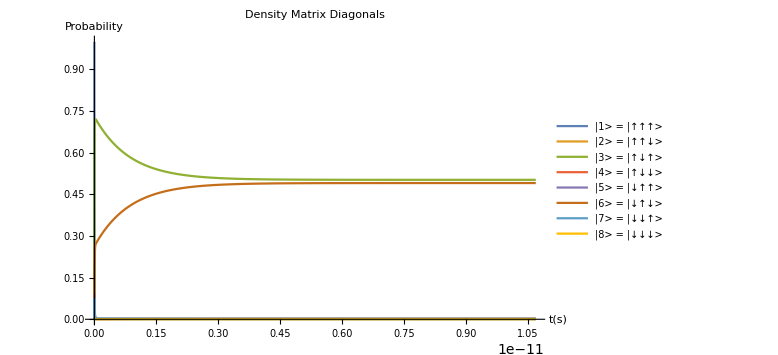

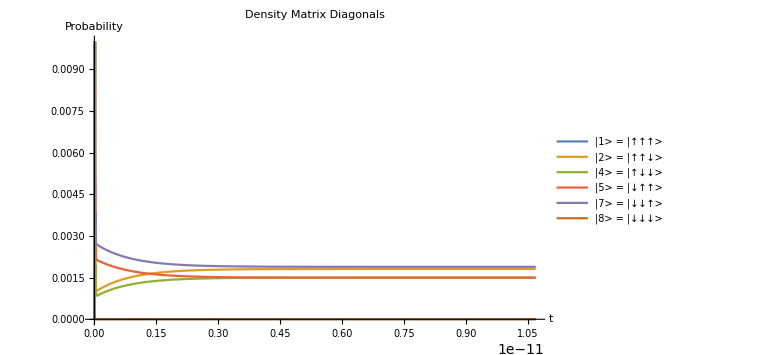

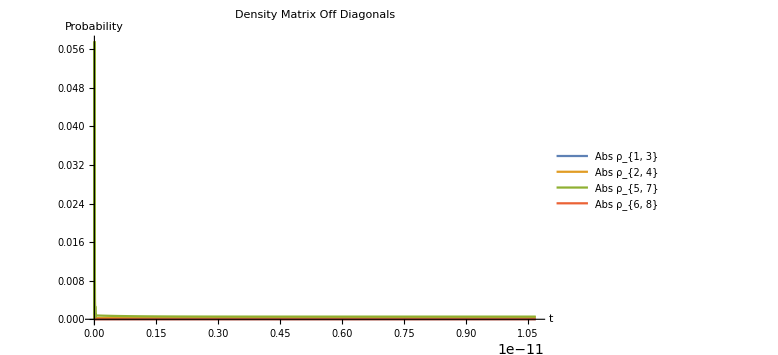

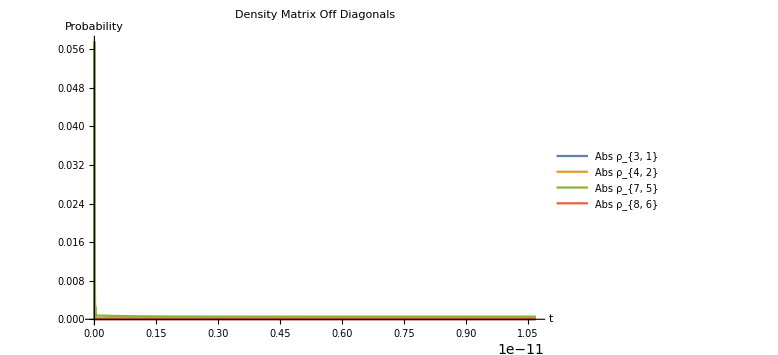

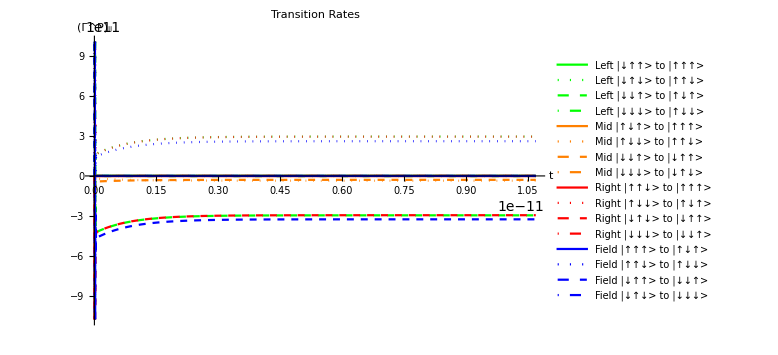

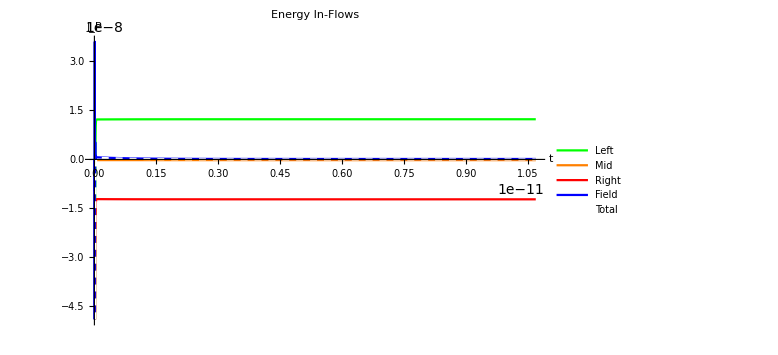

```mathematica
tmax=(2100/ωMR)//.Flatten[{unitassum,Tassum}];

dynamics=NDSolve[
Flatten[{sol//.Flatten[{Jassum,NBEassum,Tassum,unitassum,ωassum1,Ωassum}],Table[Subscript[ρ, {i,j}][0]==i,j i,1 1,{i,1,8},{j,1,8}]}]
,Flatten[Table[Subscript[ρ, {i,j}],{i,1,8},{j,1,8}]],{t,0,tmax}
];

Flatten[{Table[Subscript[ρ, {i,i}][t],{i,1,8}]}/.dynamics];
Plot[%,{t,0,tmax},PlotRange-> {0.0,1},AxesStyle->Directive[Darker[Gray],19.5,FontFamily->"Times New Roman"],ImageSize->Large,PlotLabel->  Style["Density Matrix Diagonals",19.5,FontFamily->"Times New Roman"],AxesLabel->{Style["t(s)",19.5,FontFamily->"Times New Roman"],Style["Probability",19.5,FontFamily->"Times New Roman"]}, 
PlotLegends->{
Style["|1> = |↑↑↑> ",19.5,FontFamily->"Times New Roman"],
Style["|2> = |↑↑↓> ",19.5,FontFamily->"Times New Roman"],
Style["|3> = |↑↓↑> ",19.5,FontFamily->"Times New Roman"],
Style["|4> = |↑↓↓> ",19.5,FontFamily->"Times New Roman"],
Style["|5> = |↓↑↑> ",19.5,FontFamily->"Times New Roman"],
Style["|6> = |↓↑↓> ",19.5,FontFamily->"Times New Roman"],
Style["|7> = |↓↓↑> ",19.5,FontFamily->"Times New Roman"],
Style["|8> = |↓↓↓> ",19.5,FontFamily->"Times New Roman"]}]

Flatten[{{Subscript[ρ, {1,1}][t],Subscript[ρ, {2,2}][t],Subscript[ρ, {4,4}][t],Subscript[ρ, {5,5}][t],Subscript[ρ, {7,7}][t],Subscript[ρ, {8,8}][t]}}/.dynamics];
Plot[%,{t,0,tmax},PlotRange-> {0.0,0.01},AxesStyle->Directive[Darker[Gray],19.5,FontFamily->"Times New Roman"],ImageSize->Large,PlotLabel-> Style["Density Matrix Diagonals",19.5,FontFamily->"Times New Roman"],AxesLabel->{Style["t",19.5,FontFamily->"Times New Roman"],Style["Probability",19.5,FontFamily->"Times New Roman"]}, PlotLegends->{
Style["|1> = |↑↑↑> ",19.5,FontFamily->"Times New Roman"],
Style["|2> = |↑↑↓> ",19.5,FontFamily->"Times New Roman"],
Style["|4> = |↑↓↓> ",19.5,FontFamily->"Times New Roman"],
Style["|5> = |↓↑↑> ",19.5,FontFamily->"Times New Roman"],
Style["|7> = |↓↓↑> ",19.5,FontFamily->"Times New Roman"],
Style["|8> = |↓↓↓> ",19.5,FontFamily->"Times New Roman"]}]

Flatten[{Abs[Subscript[ρ, {1,3}][t]],Abs[Subscript[ρ, {2,4}][t]],Abs[Subscript[ρ, {5,7}][t]],Abs[Subscript[ρ, {6,8}][t]]}/.dynamics];
Plot[%,{t,0,tmax},PlotRange-> Full,AxesStyle->Directive[Darker[Gray],15.5,FontFamily->"Times New Roman"],ImageSize->Large,PlotLabel-> Style["Density Matrix Off Diagonals",15.5,FontFamily->"Times New Roman"],AxesLabel->{"t","Probability"}, PlotLegends->{"Abs ρ_{1, 3}","Abs ρ_{2, 4}","Abs ρ_{5, 7}","Abs ρ_{6, 8}"}]

Flatten[{Abs[Subscript[ρ, {3,1}][t]],Abs[Subscript[ρ, {4,2}][t]],Abs[Subscript[ρ, {7,5}][t]],Abs[Subscript[ρ, {8,6}][t]]}/.dynamics];
Plot[%,{t,0,tmax},PlotRange-> Full,AxesStyle->Directive[Darker[Gray],15.5,FontFamily->"Times New Roman"],ImageSize->Large,PlotLabel-> Style["Density Matrix Off Diagonals",15.5,FontFamily->"Times New Roman"],AxesLabel->{"t","Probability"}, PlotLegends->{"Abs ρ_{3, 1}","Abs ρ_{4, 2}","Abs ρ_{7, 5}","Abs ρ_{8, 6}"}]

Flatten[
{Subscript[Τs, 1][5,1],Subscript[Τs, 1][6,2],Subscript[Τs, 1][7,3],Subscript[Τs, 1][8,4],
Subscript[Τs, 2][3,1],Subscript[Τs, 2][4,2],Subscript[Τs, 2][7,5],Subscript[Τs, 2][8,6],
Subscript[Τs, 3][2,1],Subscript[Τs, 3][4,3],Subscript[Τs, 3][6,5],Subscript[Τs, 3][8,7],
Υs[1,3],Υs[2,4],Υs[5,7],Υs[6,8]
}//.Flatten[{Jassum,NBEassum,Tassum,unitassum,ωassum1,Ωassum}]
/.dynamics];
Plot[%,{t,0,tmax},PlotRange-> Automatic,AxesStyle->Directive[Darker[Gray],15.5,FontFamily->"Times New Roman"],ImageSize->Large,PlotLabel-> Style["Transition Rates",15.5,FontFamily->"Times New Roman"],AxesLabel->{"t","(Γ^P)_ij"}, PlotLegends->{
"Left |↓↑↑> to |↑↑↑>","Left |↓↑↓> to |↑↑↓>","Left |↓↓↑> to |↑↓↑>","Left |↓↓↓> to |↑↓↓>",
"Mid |↑↓↑> to |↑↑↑>","Mid |↑↓↓> to |↑↑↓>","Mid |↓↓↑> to |↓↑↑>","Mid |↓↓↓> to |↓↑↓>",
"Right |↑↑↓> to |↑↑↑>","Right |↑↓↓> to |↑↓↑>","Right |↓↑↓> to |↓↑↑>","Right |↓↓↓> to |↓↓↑>","Field |↑↑↑> to |↑↓↑>","Field |↑↑↓> to |↑↓↓>","Field |↓↑↑> to |↓↓↑>","Field |↓↑↓> to |↓↓↓>"},PlotStyle->{{Green},{Green,Dotted},{Green,Dashed},{Green,DotDashed},{Orange},{Orange,Dotted},{Orange,Dashed},{Orange,DotDashed},{Red},{Red,Dotted},{Red,Dashed},{Red,DotDashed},{Blue},{Blue,Dotted},{Blue,Dashed},{Blue,DotDashed}}]

Flatten[{Subscript[EngyFlowIn, 1][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 3][ρMatrix[t]],EngyFlowInField[ρMatrix[t]],Subscript[EngyFlowIn, 1][ρMatrix[t]]+Subscript[EngyFlowIn, 2][ρMatrix[t]]+Subscript[EngyFlowIn, 3][ρMatrix[t]]+EngyFlowInField[ρMatrix[t]]}//.Flatten[{Jassum,NBEassum,Tassum,unitassum,ωassum1,ωassum2,Ωassum}]/.dynamics];
Plot[%,{t,0,tmax},AxesStyle->Directive[Darker[Gray],15.5,FontFamily->"Times New Roman"],AxesLabel->{"t","J_P"},ImageSize->Large,PlotLabel-> Style["Energy In-Flows",15.5,FontFamily->"Times New Roman"],PlotLegends->{"Left ","Mid","Right","Field","Total"},PlotStyle->{Green,Orange,Red,Blue,{White,Dashed}}]
```

Note - The time domain simulations show that the relaxation time of the system (amount of time the system takes to come to thermal equilibrium) is much larger than the time scales associated with the system energy levels (i.e. 1/ω_M or 1/ω_LM) for the range Ω=[0,3Δ]. This justifies the approximations we used to obtain the master equation. 
		The maximum possible τ_S value for S is associated with the smallest energy level difference between its eight eigenstates. 
		For our simulations this can be calculated to be τ_S=1/(2π ω_M) = 8×10^-15s (which corresponds to the smallest energy transitions |↓↓↑〉↔|↓↑↑〉 and |↑↑↓〉↔|↑↓↓〉 of S). 
				
		We see that at the very beginning of our graphs the density matrix elements are changing very rapidly. 
		In that small time interval the system quickly sheds the extra energy it had because of its randomly-chosen initial state.  
		Afterwards, the proper relaxation of the system to its thermal equilibrium state begins, and the state populations reaches their stationary values with a much gentler curve.  
		We can see that this relaxation time is around τ_R=5×10^-11s when Ω = 0.  For strong optical driving Ω = 3Δ, we can see that this time has reduced to around τ_R=5×10^-12s.
		
		For both cases, and therefore for values in between, we can see that the condition τ_R>>τ_S is satisfied.

Dynamics of the complete density matrix,

```mathematica
dynamics=NDSolve[
Flatten[{sol//.Flatten[{Jassum,NBEassum,Tassum,unitassum,ωassum1,Ωassum,k->1,Subscript[κ, 1]-> 1,Subscript[κ, 2]->1,Subscript[κ, 3]->1}],Table[Subscript[ρ, {i,j}][0]==i,j i,1 1,{i,1,8},{j,1,8}]}]
,Flatten[Table[Subscript[ρ, {i,j}],{i,1,8},{j,1,8}]],{t,0,tmax}
];

Manipulate[
temp=Abs[ArrayReshape[Table[Subscript[ρ, {i,j}][t],{i,1,8},{j,1,8}]/.dynamics,{8,8}]];
{ListPlot3D[temp,PlotRange->{-1,1},Mesh->6,ColorFunction->"TemperatureMap",ImageSize->Medium],DecimalForm[MatrixForm[temp],{4,3}]}
,{{t,0},0,tmax}]
```

## Density matrix, transition rate and energy flow at equilibrium

Function for density matrix elements, transition rates and energy flows,

```mathematica
varFunc[TL_,TM_,TR_,κL_,κM_,κR_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Ωs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum,ωassum1,NBEassum,unitassum,Subscript[κ, 1]-> κL,Subscript[κ, 2]->κM,Subscript[κ, 3]->κR,Ω->Ωs,Subscript[T, 1]-> TL,Subscript[T, 2]-> TM,Subscript[T, 3]-> TR,ωL->ωLs,ωM->ωMs,ωR->ωRs,ωLM->ωLMs,ωMR->ωMRs,ωRL->ωRLs}];
temp1=N[sol//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, {i_,j_}]'[t]-> 0,Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}]},1==∑_(i=1)^8 Subscript[ρ, {i,i}]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, {i,j}],{i,1,8},{j,1,8}]]]]];
Re[{Flatten[
Table[Subscript[ρ, {i,i}],{i,1,8}]/.temp3],
Flatten[{
Subscript[Τs, 1][5,1],Subscript[Τs, 1][6,2],Subscript[Τs, 1][7,3],Subscript[Τs, 1][8,4],
Subscript[Τs, 2][3,1],Subscript[Τs, 2][4,2],Subscript[Τs, 2][7,5],Subscript[Τs, 2][8,6],
Subscript[Τs, 3][2,1],Subscript[Τs, 3][4,3],Subscript[Τs, 3][6,5],Subscript[Τs, 3][8,7],
Υs[3,1],Υs[4,2],Υs[7,5],Υs[8,6]
}//.Flatten[{Subscript[ρ, {i_,j_}][t]->Subscript[ρ, {i,j}],temp0}]/.temp3],
Flatten[{
Subscript[EngyFlowIn, 1][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 3][ρMatrix[t]],EngyFlowInField[ρMatrix[t]]
}//.Flatten[{Subscript[ρ, {i_,j_}][t]->Subscript[ρ, {i,j}],ωassum2,temp0}]/.temp3]}]
]
```

Comparison of the answers from both unit conventions,

```mathematica
Module[{t1,t2,unitassumt},
unitassumt= {k-> 1,ℏ->1};
t1=varFunc[0.2,0.02,0.02,1,1,1,0,0.1,0,1,1,0,0,unitassumt];
unitassumt=  unitassum;
t2=varFunc[0.2 Tconv,0.02 Tconv,0.02 Tconv,1,1,1,0 ωconv,0.1 ωconv,0 ωconv,1 ωconv,1 ωconv,0 ωconv,0 ωconv,unitassumt];
Quiet[MapThread[#1/#2 &,{t2,t1}]]
]
Module[{t1,t2,unitassumt},
unitassumt= {k-> 1,ℏ->1};
t1=varFunc[0.2,0.02,0.02,1,1,1,0,0.1,0,1,1,0,0.3,unitassumt];
unitassumt=  unitassum;
t2=varFunc[0.2 Tconv,0.02 Tconv,0.02 Tconv,1,1,1,0 ωconv,0.1 ωconv,0 ωconv,1 ωconv,1 ωconv,0 ωconv,0.3 ωconv,unitassumt];
Quiet[MapThread[#1/#2 &,{t2,t1}]]
]
( (Tconv k)/ℏ)/.unitassum
( (Tconv k)^2/ℏ)/.unitassum
```

{{1.,1.,1.,1.,1.,1.,1.,1.},{1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{4.06659×10^-6,4.06659×10^-6,4.06659×10^-6,Indeterminate}}

{{1.,1.,1.,1.,1.,1.,1.,1.},{1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,1.96368×10^14,Indeterminate,1.96368×10^14,1.96368×10^14,Indeterminate},{4.06659×10^-6,4.06659×10^-6,4.06659×10^-6,4.06659×10^-6}}

1.96368×10^14

4.06659×10^-6

Function for drawing a state flow diagram,

```mathematica
DrawFlowGraph[label_,posx_,posy_,nodes_,rates_,ratecolors_,ratesF_,ratecolorsF_,title_,maxrate_]:=Module[{pos,psize},
psize=Dimensions[label][[1]];
pos[i_]:={posx[[i]],posy[[i]]};
Graphics[Flatten[{
{Thickness[0.0001],Arrowheads[0.03],Black,Arrow[{{1.15Min[posx],1.2Min[posy]},{1.15Min[posx],1.1Max[posy]}}]},Black,{Text[Style["Energy",FontSize->13.6,FontFamily->"Times New Roman"],{1.0Min[posx]-0.03,1.15Max[posy]}],Text[Style[title,FontSize->13.6,FontFamily->"Times New Roman"],{0,1.27Min[posy]}]},
Table[{Opacity[1],Thick,RGBColor[0.08,0.56,1],Disk[pos[i],0.01+0.22 √nodes[[i]]]},
{i,1,psize}],
Table[
If[rates[[i,j]]≠0 ,
If[ratesF[[i,j]]≠0,
If[Abs[rates[[i,j]]]>Abs[ratesF[[i,j]]],
{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
Opacity[1],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]},
{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
Opacity[1],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
],
{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
],Nothing]
,{i,1,psize-1},{j,i+1,psize}],
Table[{Opacity[1],Black,Text[Style[label[[i]],FontSize->12],{posx[[i]]+{0,0.04,0,0.06,0.04,0,0.04,0}[[i]],posy[[i]]+{0.045,0.08,-0.05,-0.06,0.06,-0.05,-0.08,0.045}[[i]]}]},{i,1,psize}]

}], ImageSize->Medium]
]

DrawFunc[TL_,TM_,TR_,κL_,κM_,κR_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,title_,maxrate_,var_]:=Module[{label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF},temp0=Flatten[{Jassum,ωassum1,NBEassum,k->1,Subscript[κ, 1]->κL,Subscript[κ, 2]->κM,Subscript[κ, 3]->κM,Subscript[T, 1]-> TL,Subscript[T, 2]-> TM,Subscript[T, 3]-> TR,ωL->ωLs,ωM->ωMs,ωR->ωRs,ωLM->ωLMs,ωMR->ωMRs,ωRL->ωRLs}];label={"|↑↑↑>","|↑↑↓>","|↑↓↑>","|↑↓↓>","|↓↑↑>","|↓↑↓>","|↓↓↑>","|↓↓↓>"};posx={0.15,-0.4,0.15,0.45,0.6,-0.15,-0.6,-0.15};posy=Table[Subscript[ω, i]/ωconv,{i,1,8}]//.Flatten[{ωassum2,temp0}];nodes=var[[1]];rates=({{0, -var[[2]][[9]], -var[[2]][[5]], 0, -var[[2]][[1]], 0, 0, 0}, {0, 0, 0, -var[[2]][[6]], 0, -var[[2]][[2]], 0, 0}, {0, 0, 0, -var[[2]][[10]], 0, 0, -var[[2]][[3]], 0}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[4]]}, {0, 0, 0, 0, 0, -var[[2]][[11]], -var[[2]][[7]], 0}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[8]]}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[12]]}, {0, 0, 0, 0, 0, 0, 0, 0}});
ratesF=({{0, 0, -var[[2]][[13]], 0, 0, 0, 0, 0}, {0, 0, 0, -var[[2]][[14]], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -var[[2]][[15]], 0}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[16]]}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});ratecolors=({{0, Red, Orange, 0, Green, 0, 0, 0}, {0, 0, 0, Orange, 0, Green, 0, 0}, {0, 0, 0, Red, 0, 0, Green, 0}, {0, 0, 0, 0, 0, 0, 0, Green}, {0, 0, 0, 0, 0, Red, Orange, 0}, {0, 0, 0, 0, 0, 0, 0, Orange}, {0, 0, 0, 0, 0, 0, 0, Red}, {0, 0, 0, 0, 0, 0, 0, 0}});
ratecolorsF=({{0, 0, Blue, 0, 0, 0, 0, 0}, {0, 0, 0, Blue, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, Blue, 0}, {0, 0, 0, 0, 0, 0, 0, Blue}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
DrawFlowGraph[label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,title,maxrate]
]
```

Simulation for natural units

```mathematica
unitassum = {k-> 1,ℏ->1};
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

Simulation for SI units

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
Tconv=300/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
```

Steady-state energy flows, transition rates, density matrix diagonals and energy eigenvalues, plotted for dynamically changeable bath, field and system parameters,

```mathematica
Manipulate[Module[{temp},
temp=varFunc[TL,TM,TR,κL,κM,κR,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωs,unitassum];
{
DrawFunc[TL,TM,TR,κL,κM,κR,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,StringForm["Ω=``",Ωs],Τmax,temp],

BarChart[temp[[3]]
,ChartLabels->{"Left ","Mid","Right","Field"},PlotLabel->"Equilibrium energy inflow",AxesLabel->{"","J_P(J)"},ImageSize->Medium,PlotRange->{-Emax,Emax},ChartStyle->{Green,Orange,Red,Blue}],

BarChart[temp[[2]]
,ChartLabels->Placed[{"L |↓↑↑> to |↑↑↑>","L |↓↑↓> to |↑↑↓>","L |↓↓↑> to |↑↓↑>","L |↓↓↓> to |↑↓↓>","M |↑↓↑> to |↑↑↑>","M |↑↓↓> to |↑↑↓>","M |↓↓↑> to |↓↑↑>","M |↓↓↓> to |↓↑↓>","R |↑↑↓> to |↑↑↑>","R |↑↓↓> to |↑↓↑>","R |↓↑↓> to |↓↑↑>","R |↓↓↓> to |↓↓↑>","F |↓↑↑> to |↓↓↑>"},Center,Rotate[#,π/2]&],PlotLabel->"Equilibrium thermal transition rate",ImageSize->Medium,ChartStyle->{Green,Green,Green,Green,Orange,Orange,Orange,Orange,Red,Red,Red,Red,Blue}],

BarChart[temp[[1]]
,ChartLabels->{"ρ_{1, 1}","ρ_{2, 2}","ρ_{3, 3}","ρ_{4, 4}","ρ_{5, 5}","ρ_{6, 6}","ρ_{7, 7}","ρ_{8, 8}"},PlotLabel->"Equilibrium density matrix",ImageSize->Medium,PlotRange->{-0.1,1},ChartStyle->"Pastel"]
}],
{{TL,0.20 Tconv},0.001 Tconv,1 Tconv},
{{TM,0.02 Tconv},0.001 Tconv,1 Tconv},
{{TR,0.02 Tconv},0.001 Tconv,1 Tconv},
{{κL,1},0.01,10},
{{κM,0.1},0.01,10},
{{κR,1},0.01,10},
{{ωLs,0.0ωconv},0ωconv,2ωconv},
{{ωMs,0.0ωconv},0ωconv,2ωconv},
{{ωRs,0.0ωconv},0ωconv,2ωconv},
{{ωLMs,1.1ωconv},0ωconv,2ωconv},
{{ωMRs,0.9ωconv},0ωconv,2ωconv},
{{ωRLs,0ωconv},0ωconv,2ωconv},
{{Ωs,0.3ωconv},0ωconv,5ωconv},
{{Emax,0.0034Econv},0.00001Econv,0.005Econv},
{{Τmax,0.006Τconv},0.0001Τconv,0.02Τconv}]
```

Function for more quickly calculating the inwards energy flows,

```mathematica
varEngyFunc[TL_,TM_,TR_,κL_,κM_,κR_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Ωs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum,ωassum1,NBEassum,unitassum,Subscript[κ, 1]-> κL,Subscript[κ, 2]->κM,Subscript[κ, 3]->κR,Ω->Ωs,Subscript[T, 1]-> TL,Subscript[T, 2]-> TM,Subscript[T, 3]-> TR,ωL->ωLs,ωM->ωMs,ωR->ωRs,ωLM->ωLMs,ωMR->ωMRs,ωRL->ωRLs}];
temp1=N[sol//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, {i_,j_}]'[t]-> 0,Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}]},1==∑_(i=1)^8 Subscript[ρ, {i,i}]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, {i,j}],{i,1,8},{j,1,8}]]]]];
Re[Flatten[{
Subscript[EngyFlowIn, 1][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 3][ρMatrix[t]],EngyFlowInField[ρMatrix[t]]
}//.Flatten[{Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}],ωassum2,temp0}]/.temp3]]
]
```

Callout::copos: Axis is not a valid position for the placement of callouts.

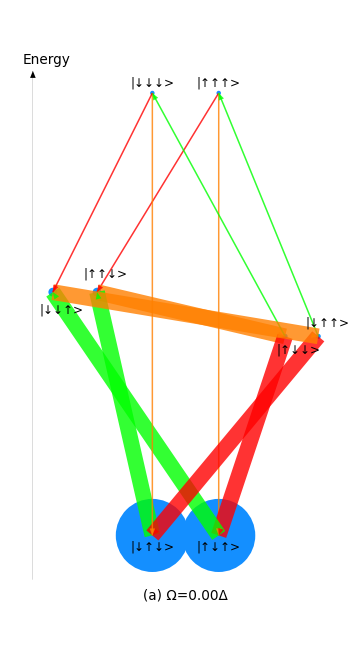
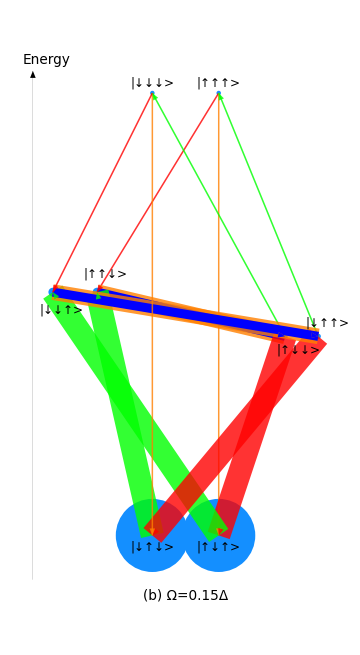
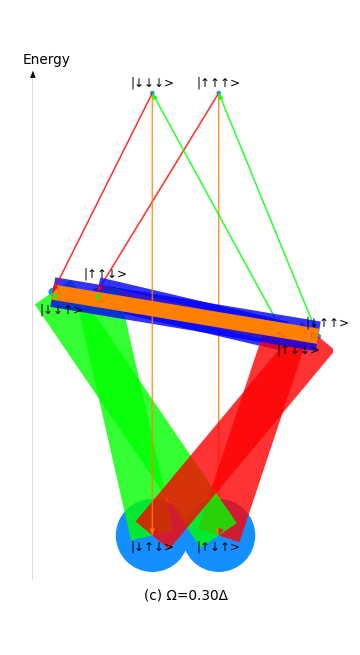
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{TL,TM,TR,κL,κM,κR,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωs,temp1,temp2,temp3},
TL=0.2Tconv;TM=0.02Tconv;TR=0.02Tconv;
κL=1;κM=0.1;κR=1;
ωLs=0ωconv;ωMs=0ωconv;ωRs=0ωconv;
ωLMs=1.1ωconv;ωMRs=0.9ωconv;ωRLs=0ωconv;
Ωs=0ωconv;
temp1=varFunc[TL,TM,TR,κL,κM,κR,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωs,unitassum];

TL=0.2Tconv;TM=0.02Tconv;TR=0.02Tconv;
κL=1;κM=0.1;κR=1;
ωLs=0ωconv;ωMs=0ωconv;ωRs=0ωconv;
ωLMs=1.1ωconv;ωMRs=0.9ωconv;ωRLs=0ωconv;
Ωs=0.15ωconv;
temp2=varFunc[TL,TM,TR,κL,κM,κR,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωs,unitassum];

TL=0.2Tconv;TM=0.02Tconv;TR=0.02Tconv;
κL=1;κM=0.1;κR=1;
ωLs=0ωconv;ωMs=0ωconv;ωRs=0ωconv;
ωLMs=1.1ωconv;ωMRs=0.9ωconv;ωRLs=0ωconv;
Ωs=0.3ωconv;
temp3=varFunc[TL,TM,TR,κL,κM,κR,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωs,unitassum];
{
DrawFunc[TL,TM,TR,κL,κM,κR,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,"(a) Ω=0.00Δ",0.0014Τconv,temp1],
DrawFunc[TL,TM,TR,κL,κM,κR,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,"(b) Ω=0.15Δ",0.0014Τconv,temp2],
DrawFunc[TL,TM,TR,κL,κM,κR,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,"(c) Ω=0.30Δ",0.0014Τconv,temp3],
BarChart[10^9{temp1[[3]],temp2[[3]],temp3[[3]]},ChartLabels->{Callout[{
Style["Ω=0.00Δ",FontSize->13.5,FontFamily->"Times New Roman",FontColor->Darker[Gray]],
Style["Ω=0.15Δ",FontSize->13.5,FontFamily->"Times New Roman",FontColor->Darker[Gray]],
Style["Ω=0.30Δ",FontSize->13.5,FontFamily->"Times New Roman",FontColor->Darker[Gray]]},Automatic,CalloutStyle->Darker[Gray]],Placed[{
Style["J_L",FontSize->13.5,FontColor->Darker[Gray],FontFamily->"Times New Roman"],
Style["J_M",FontSize->13.5,FontColor->Darker[Gray],FontFamily->"Times New Roman"],
Style["J_R",FontSize->13.5,FontColor->Darker[Gray],FontFamily->"Times New Roman"],
Style["J_F",FontSize->13.5,FontColor->Darker[Gray],FontFamily->"Times New Roman"]},Axis]},AxesOrigin->{0,0},Axes->{True,True},AxesStyle->Directive[Darker[Gray],12,FontFamily->"Times New Roman"],AxesLabel->{"",
Style["J_P(10^-9 J)",FontSize->13.5,FontFamily->"Times New Roman"]},ImageSize->Medium,ChartStyle->{Green,Orange,Red,Blue},BarSpacing->{Small,1}]
}]
```